```mathematica
data=ReadList["C:\Laboratory\Projects\Ailove-Instagram\stat-py\out.txt",{Real, Real}]
```

{{55.747,37.5462},{55.7642,37.574},{55.752,37.5659},{55.7958,37.5408},{55.7782,37.6535},«10198»,{55.7645,37.617},{55.7595,37.6092},{55.7495,37.6068},{55.7573,37.6131},{55.7352,37.6435}}

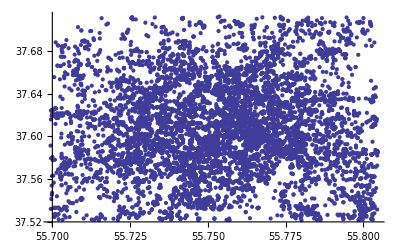

{{{55.747,37.5462},{55.7531,37.5445},{55.7531,37.5445},{55.7419,37.5438},{55.7478,37.5492},«111»,{55.7389,37.5401},{55.7442,37.5454},{55.7461,37.547},{55.7472,37.5452}},«498»,{{55.745,«12»}}}

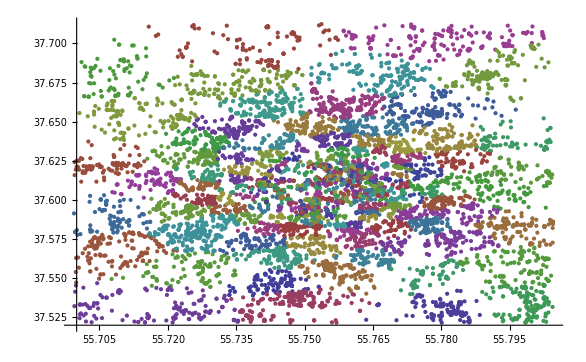

Read::readt: Invalid input found when reading "latitude, longitude,timestamp, id\n" from "C:\\Laboratory\\Projects\\Ailove-Instagram\\stat-py\\out.csv".

{$Failed}

ReadList::nffil: File not found during ReadList["out.csv"].

$Failed

```mathematica
ListPlot[data]
cl=FindClusters[data,500]
ListPlot[cl]
```